# .7fLinear Regression by Folding

Brian Beckman
12 Feb 2018

## Introduction

Linear systems appear everywhere, and, where they don’t appear naturally, linear approximations abound because non-linear systems are often intractable. Examples comprise machine learning, control systems, dynamics, robotics, and many more.

Linear regression is the standard technique for estimating the parameters or coefficients of a linear system. Usually, authors sweep linear regression under the rug, presumably because readers know all about effective ways to perform it. However, I have found this presumption not to be true. Time and again, I see code that employs the normal equations directly (that's inefficient), computes matrix inverses (that's risky), or abuses neural nets (a sledgehammer) to open a walnut (linear regression).

This paper shows an efficient, reliable method for very general linear regression. The method is mathematically equivalent to a Kalman fold for static systems. It is amongst the best known methods for linear regression.

## Motivating Example

Find best-fit, unknowns m, b, where z≈m x+b, given known data (z_1,z_2,…,z_k) and (x_1,x_2,…,x_k). Write this system as a matrix equation and remember the symbols Ζ (observations, known), A (partials, known), and Ξ (model, state, unknown parameters to be estimated). Rows of Ζ and A come in matched pairs.

Ζ_(k×1)  =  (z_1
z_2
⋮
z_k)  =  (x_1 | 1
x_2 | 1
⋮ | ⋮
x_k | 1)·(m
b) + noise  =  A_(k×2)·Ξ_(2×1)+samples of NormalDistribution[0,σ_Ζ]

This extends to any linear system with any number of parameters.7f and with tensors in the matrix slots; extended example below.

Ground Truth

Test the method as follows: make some data by sampling a line specified by ground truth m and b, then adding some noise. Run the faked data through our estimation procedures and see how close the estimates come to the ground truth. In the real world, we don’t know ground truth, so it’s paramount that we trust the method before deploying it. Build up trust by testing.

```mathematica
ClearAll[groundTruth,m,b];
groundTruth={m,b}={0.5,-1./3.};
```

Partials

The partials A are a (column) vector of co-vectors (row vectors). Each co-vector is the gradient of the observation model, namely of A·Ξ, with respect to Ξ, evaluated at a specific Ξ. Gradients are co-vectors, that is, linear transformations of vectors. This fact drives  the dual problem, below.

```mathematica
ClearAll[nData,min,max];
nData=119;min=-1.;max=3.;
ClearAll[partials];
partials=Array[{#,1.0}&,nData,{min,max}];
Short[partials,3]
```

{{-1.,1.},{-0.966102,1.},«115»,{2.9661,1.},{3.,1.}}

Fake Data

```mathematica
ClearAll[fake];
fake[n_,σ_,A_,{m_,b_}]:=
Table[
RandomVariate[NormalDistribution[0,σ]]+A⟦i⟧.{m,b},
{i,n}];
```

```mathematica
ClearAll[data,noiseSigma];
noiseSigma=0.65;
data=fake[nData,noiseSigma,partials,groundTruth];
Short[data,3]
```

{-2.46481,-2.25988,-0.807362,«114»,0.940923,2.26875}

Model

Try the Wolfram built-in. The estimated m and b are reasonably close to the ground truth.

```mathematica
ClearAll[model];
model=LinearModelFit[{partials⟦All,1⟧,data}ᵀ,ξ,ξ];
Normal[model]
```

-0.399214+0.582442 ξ

Un-comment the following line to see everything Wolfram has to say about this model (it’s a lot of data).

```mathematica
(*Association[(#->model[#])&/@model["Properties"]]*)
```

The plot shows that Wolfram does an acceptable job of estimating the parameters m and b that define the line:

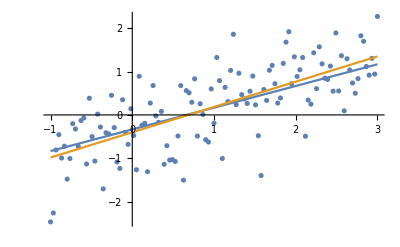

```mathematica
Show[ListPlot[{partials⟦All,1⟧,data}ᵀ],
Plot[{m ξ+b,model[ξ]},{ξ,min,max}]]
```

In the following, we show several methods that are all mathematically equivalent to each other, but have vastly different operational characteristics regarding memory usage and numerical risk.

Normal Equations

Equation 1 can be solved for a value of Ξ that minimizes the square error J(Ξ)=^def(Ζ-A·Ξ)ᵀ·(Ζ-A·Ξ). Because the noise 𝒩(0,σ) has zero mean (or zero bias), The solution turns out to be exactly what one would get from naive algebra.  Aᵀ·A is square. When it is invertible,

(Aᵀ·A)^-1·Aᵀ·Z  =  Ξ

That gives the same answer as Wolfram’s built-in:

```mathematica
Inverse[partialsᵀ.partials].partialsᵀ.data
```

{0.582442,-0.399214}

The matrix (Aᵀ·A)^-1·Aᵀ is the Moore-Penrose left pseudoinverse. Wolfram has a built-in for it:

```mathematica
PseudoInverse[partials].data
```

{0.582442,-0.399214}

(Aᵀ·A)^-1·Aᵀ·Ζ is a very nasty computation at scale: in memory usage, in time, and in numerical risk. Eliminate these defects with a recurrence. This recurrence is mathematically identical to a Kalman filter in parameter-estimation mode, though we do not prove that here.

## Recurrence

Fold the following recurrence over Ζ and A:

ψ←(Λ+aᵀ·a)^-1·(aᵀ·ζ+Λ·ψ)
Λ←(Λ+aᵀ·a)

where ψ is the current estimate of Ξ, a and ζ are matched rows of A and Ζ, and Λ accumulates Aᵀ·A.

Derive the recurrence as follows: Treat the estimate-so-far, ψ, as just one more observation with information matrix (proportional to inverse covariance) Λ=A_(so-far)ᵀ·A_(so-far). The scalar performance or squared error of the estimate, so far, is J(x)=(z-A_(so-far)·x)ᵀ·(z-A_(so-far)·x)=(x-ψ)ᵀ·Λ·(x-ψ), where x is the unknown true parameter vector and Λ=Aᵀ·A. Adding a new observation, ζ and its corresponding partial a, increases the error by (ζ-a·x)ᵀ·(ζ-a·x). Minimize the new total error with respect to x to get the recurrence.

We must bootstrap the recurrence with initial values of ψ and Λ, namely ψ_0 and Λ_0. The initial value of ψ does not matter much, but the initial value of Λ cannot be singular. For practical purposes, any Λ_0 with terms much smaller than typical terms in Aᵀ·A will do. The example below starts with ψ_0=(0 | 0)ᵀ and Λ_0=((10^-6 | 0)(0 | 10^-6)).

```mathematica
ClearAll[update];
update[{ψ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{Inverse[Π].(aᵀ.ζ+ Λ.ψ),Π}];
MatrixForm/@
({({{mBar}, {bBar}}),Π}=Fold[update,
{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@data,List/@partials}ᵀ])
```

{(0.582442
-0.399214),(280.356 | 119.
119. | 119.)}

The estimates mBar and bBar are exactly what we got from Wolfram’s built-in.

The mappings of List over the data and partials convert them into column vectors, as required by the recurrences in linear-algebra form. The earlier applications of Wolfram built-ins and the normal equations are more loose: they (promiscuously) treat a simple list as a column vector. Python’s numpy has the same dubious feature. I call it dubious because the looseness inhibits disciplined extension to higher dimensions and to tensorial data. If we are scrupulous in expressing column vectors as tall matrices and co-vectors as flat matrices, we have an easier time with such extensions. Now that we know, we just pay attention.

We might also fold this recurrence over an asynchronous stream, in which case it runs in constant memory, O(n), where n is the dimension (length) of Ξ, same as the dimension of each row of A.

The final value of Λ (called Π in the code, a returned value), is A_full ᵀ·A_full+Λ_0:

```mathematica
Π-partialsᵀ.partials
```

{{1.×10^-6,0.},{0.,1.×10^-6}}

The covariance of the estimate Ξ is ((n-1)/(n-2))*Variance[Ζ-A·Ξ]*Λ^-1 except for a small contribution from the a-priori covariance Λ_0. The correction factor ((n-1)/(n-2)) is a generalization .7fof Bessel’s correction. The 2 in (n-2) in the denominator is due to the fact that we’re estimating two parameters from the data (see VAN DE GEER, Least Squares Estimation, Volume 2, pp. 1041–1045, in Encyclopedia of Statistics in Behavioral Science, Eds. Brian S. Everitt & David C. Howell, Wiley, 2005). The denominator of the correction, in general, is n-p, where n is the number of data and p is the number of parameters being estimated.

```mathematica
Inverse[partialsᵀ.partials]*(nData-1)/(nData-2)*Variance[data-partials.{mBar,bBar}]//MatrixForm
```

(0.00267701 | -0.00267701
-0.00267701 | 0.00630684)

Except for the reversed order, this is the same covariance matrix that Wolfram reports:

```mathematica
Reverse@(Reverse/@model["CovarianceMatrix"])//MatrixForm
```

(0.00267701 | -0.00267701
-0.00267701 | 0.00630684)

Don’t Invert That Matrix.7f

See https://www.johndcook.com/blog/2010/01/19/dont-invert-that-matrix/

In general, when you see a matrix expression A^-1·B, you may (and should) replace it with linsolve(A,B).

Replace Inverse with LinearSolve:

```mathematica
ClearAll[update];
update[{ψ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{LinearSolve[Π,(aᵀ.ζ+Λ.ψ)],Π}];
MatrixForm/@({({{mBar}, {bBar}}),Π}=Fold[update,
{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@data,List/@partials}ᵀ])
```

{(0.582442
-0.399214),(280.356 | 119.
119. | 119.)}

exactly as before.

We have eliminated memory bloat by accumulating estimate updates one observation at a time, each with its paired partial. We reduce computation time and numerical risk by solving a linear system instead of inverting a matrix.

## The Dual Problem

When the model --- the thing we’re trying to estimate --- is a co-vector (row-vector), e.g., a gradient, we have the dual (transposed) problem. In that case, the observations Ω and the model Γ are now.7f co-vectors with elements ω and γ  instead of ζ and ψ. The co-partials Θ (replacing A) are now a co-vector of column vectors θ. The observation equation looks like Ω=Γ·Θ and the error-so-far like (x-γ)·Λ·(x-γ)ᵀ, where Λ=Θ_(so-far)·Θ_(so-far)ᵀ. We don’t change the name of Λ because it’s symmetric. Adding a new observation ω introduces new error (ω-x·θ)·(ω-x·θ)ᵀ. Minimizing the total error yields

γ←(γ·Λ+ω·θ ᵀ ).(Λ+θ·θ ᵀ )^-1
Λ←(Λ+θ·θ ᵀ )

LinearSolve operates on the transposed right-hand side of the recurrence, and we transpose the solution to get the recurrence. We apply this dual model to the transpose of the original data:

```mathematica
Transpose/@List/@partials⟦1;;3⟧
```

{{{-1.},{1.}},{{-0.966102},{1.}},{{-0.932203},{1.}}}

```mathematica
ClearAll[coUpdate];
coUpdate[{γ_,Λ_},{ω_,θ_}]:=
With[{Π=(Λ+θ.θᵀ)},
{LinearSolve[Π,Λ.γᵀ+θ.ωᵀ]ᵀ,Π}];
MatrixForm/@Fold[
coUpdate,
{({{0, 0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@List/@data,Transpose/@List/@partials}ᵀ]
```

{(0.582442 | -0.399214),(280.356 | 119.
119. | 119.)}

Application of the Dual Problem

Imagine a scalar function J(θ) of a column K-vector θ_(K×1). We want to estimate its gradient co-vector ∇J, given a batch of ℐ random increments ΔΘ_(K×ℐ), from the system ∇J·ΔΘ=Δ J. Here, ∇J takes the role of the model whose state parameters Γ we want to estimate, ΔΘ takes the role of the partials of the model w.r.t. those parameters, and Δ J takes the role of measured data. Let Δ J_(ℐ×1) be a batch of observed increments to J and ΔΘ_(K×ℐ) be a matrix of the ℐ corresponding column-vector random increments to the input vectors θ_(K×1). The right pseudoinverse RPI=^def(ΔΘ_(K×ℐ)·ΔΘ_(K×ℐ)^ᵀ)^-1·ΔΘ_(K×ℐ)^ᵀ solves ∇ J_(ℐ×1)·ΔΘ_(K×ℐ)=Δ J_(ℐ×1) to yield ∇ J_(ℐ×1)≈Δ J_(ℐ×1)·RPI. Use the co-update recurrence for this problem.

## A Longer Example

Chris Bishop’s book Pattern Recognition and Machine Learning has an extended example, starting in section 1.1, that segues into regularization as a cure for overfitting.

This time, we produce the data in the correct, column-vector form at the outset so we don’t need to reshape it later.

```mathematica
ClearAll[bishopTrainingSetX];
bishopTrainingSetX[n_]:=Array[#&,n,{0.,1.}];
```

```mathematica
ClearAll[bishopFakeY,bishopGroundTruthY];
bishopGroundTruthY[xs_]:=Sin[2.π#]&/@xs;
bishopFakeY[xs_,σ_]:=
With[{n=Length@xs},
bishopGroundTruthY[xs]
+RandomVariate[NormalDistribution[0.,σ],n]];
```

```mathematica
ClearAll[bishopTrainingSet,bishopFake];
bishopFake[n_,σ_]:=
With[{xs=bishopTrainingSetX[n]},
With[{ys=bishopFakeY[xs,σ]},
{xs,ys}]];
bishopTrainingSet=bishopFake[10,0.25];
```

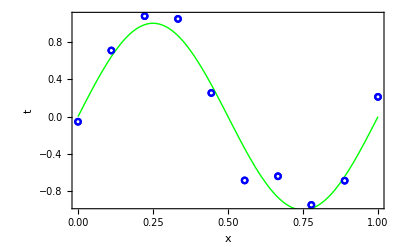

```mathematica
With[{lp=ListPlot[bishopTrainingSetᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,(* once to set scale *)
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
lp (* once to overdraw the plot *)},
Frame->True,
FrameLabel->{"x","t"}]]
```

## Regularization and MAP